# -Graphics-

# Wolfram Language Basics

## Visualization and graphics

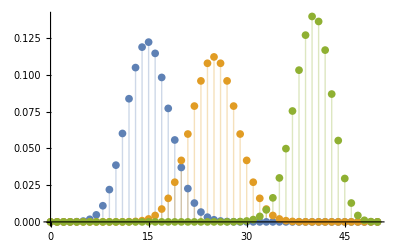

## Outline

### An Introduction to the Graphics and Visualization Features of the Wolfram Language^TM

Function visualization in two and three dimensions

Data visualization in two and three dimensions

Graphics options

Functions for displaying graphics and graphics grids

Dynamic and interactive graphics

## Function Visualization: Overview

Functions of one and two variables—Plot, LogPlot, LogLogPlot, Plot3D

Parametric curves in two and three dimensions—ParametricPlot, ParametricPlot3D

Regions defined by inequalities—RegionPlot, RegionPlot3D

Density and contour plots—DensityPlot, ContourPlot, ContourPlot3D, …

Vector and stream visualization—VectorPlot, VectorPlot3D, StreamPlot, StreamDensityPlot, LineIntegralConvolutionPlot, …

Other plotting functions—DiscretePlot, PolarPlot, …

## Basic Plots

Plot is used to generate plots of functions of one variable:

```mathematica
Plot[Sinc[x],{x,-3π,3π}]
```

To plot several functions together, put them in a list as the first argument to Plot:

```mathematica
Plot[{Sin[x],2 Sin[2 x],1/3 Sin[3 x]},{x,0,2 π}]
```

Note that Plot automatically displays each function with a unique color.

## Plotting Parametric Functions

You can also plot functions in which both coordinates are given in terms of a third parameter. Such functions are said to be given parametrically and can be plotted with ParametricPlot.

For example, here is a plot of a function in which the x coordinate is given by cos(3t) and the y coordinate is given by sin(5t) where t varies from 0 to 2π:

```mathematica
ParametricPlot[{Cos[3t],Sin[5t]},{t,0,2π}]
```

## Plotting a Surface

The Plot3D function plots a function as a three-dimensional surface:

```mathematica
Plot3D[Sin[x-Sin[y]],{x,0,3 π},{y,0,4 π}]
```

To rotate this graphic, move the cursor over the graphic, hold down the left mouse button, and then rotate the image by moving the mouse.

To zoom, hold down the keys indicated in the table and when the small set of coordinate axes appears at the bottom of your cursor, move the cursor over the graphic, and then drag the pointer up to zoom in and down to zoom out.

| macOS | Windows, Linux/Unix
Rotate | drag and rotate pointer | drag and rotate pointer
Zoom | use Command (⌘) key | use Control (Ctrl) key
Pan | use Shift (Shift) key | use Shift (Shift) key

Just like Plot, you can combine surfaces in one graphic by enclosing functions in a list as the first argument to Plot3D:

```mathematica
Plot3D[{Sin[x-Sin[y]],Sin[y-Cos[x]]},{x,0,3π},{y,0,4π}]
```

The two surfaces might be easier to discern if they were colored differently:

```mathematica
Plot3D[{Sin[x-Sin[y]],Sin[y-Cos[x]]},{x,0,3π},{y,0,4π},PlotStyle->{Yellow,Cyan}]
```

## Space Curves and Parametric Surfaces

Here is a three-dimensional space curve parameterized by the variable t that ranges from 0 to 6π:

```mathematica
ParametricPlot3D[{t/5,Sin[t], Cos[t]},{t,0,6π}]
```

## Contour and Density Plots

Functions of two variables can also be visualized using density and contour plots:

```mathematica
DensityPlot[Sin[x-Sin[y]],{x,0,3π},{y,-π,π}]
```

Note that as you hover your mouse over the contours, a tooltip appears, displaying the value of each contour:

```mathematica
ContourPlot[Sin[x-Sin[y]],{x,0,3π},{y,-π,π}]
```

## Log Plots

Using LogPlot, you can make plots of functions of one variable on a logarithmic scale along the y axis.

For example, here is a plot of several exponential functions plotted on “log paper”:

```mathematica
LogPlot[{2^x,3^x,4^x},{x,1,8}]
```

You can plot with a logarithmic x scale by using LogLinearPlot:

```mathematica
LogLinearPlot[Log[x],{x,1,8}]
```

Or use log-log scales:

```mathematica
LogLogPlot[Tooltip[{Log[x],x,x^2,E^x}],{x,1,100}]
```

## Plotting Regions Defined by Inequalities

It is often convenient to plot regions defined by inequalities. For example, this plots the upper half of an ellipse:

```mathematica
RegionPlot[x^2/9+y^2/4≤1,{x,-3,3},{y,0,2}]
```

You can combine several inequalities using logical operators:

```mathematica
RegionPlot[1≤x^2+2 y^2≤4||1≤3 (x-1)^2+(y-1)^2≤4,{x,-2,3},{y,-2,3}]
```

RegionPlot3D is used to plot solids, specified by inequalities. It is important to note that RegionPlot3D operates on volumes and not on surfaces, so it can miss details that you might wish to capture.

```mathematica
RegionPlot3D[x^2+y^2+z^2>1&&x+y-z≤2,{x,-1,1},{y,0,1},{z,-1,1}]
```

## Vector Visualization

Plot vector fields using VectorPlot:

```mathematica
VectorPlot[{1-x^2-y,1-x-y^2},{x,-3,3},{y,-3,3}]
```

You can plot streamlines with arrows representing the field:

```mathematica
StreamPlot[{1-x^2-y,1-x-y^2},{x,-3,3},{y,-3,3}]
```

Plot a 3D vector field:

```mathematica
VectorPlot3D[{Cos[x],Sin[y],z},{x,-1,1},{y,-1,1},{z,-1,1}]
```

Compare vector field visualization functions:

```mathematica
Manipulate[f[{-1-x^2+y,1+x-y^2},{x,-3,3},{y,-3,3},PlotLabel->f],{f,{VectorPlot,VectorDensityPlot,StreamPlot,StreamDensityPlot,LineIntegralConvolutionPlot}}]
```

## Other Functions

Use PolarPlot to plot curves where the radius is given as a function of angle θ:

```mathematica
PolarPlot[Sin[5θ],{θ,0,π}]
```

DiscretePlot is used to plot an expression for discrete values:

```mathematica
DiscretePlot[PDF[BinomialDistribution[50,0.5],k],{k,0,50}]
```

Revolve a curve around the z axis:

```mathematica
RevolutionPlot3D[t^4-t^2,{t,0,1}]
```

Plot in spherical coordinates:

```mathematica
SphericalPlot3D[{1,2,3,4},{θ,0,π},{ϕ,0,(3 π)/2},PlotStyle->Opacity[0.75]]
```

## Syntax

All plotting functions use similar syntax:

```mathematica
Plot[Sin[x],{x,0,2π}]
```

```mathematica
Plot[{Sin[x]/2,ⅇ^(-x^2)},{x,-π,π}]
```

```mathematica
LogPlot[(1+x^4)/(1+x^2),{x,-2,10}]
```

```mathematica
Plot3D[Sin[x] Sin[y],{x,0,2 π},{y,0,2 π}]
```

```mathematica
ContourPlot[Sin[x] Sin[y],{x,0,2 π},{y,0,2 π}]
```

The first argument gives the function or a list of functions to plot.

A list {x,xmin,xmax} is used to specify the name and the range of each variable.

## Data Visualization: Overview

Plotting data in two and three dimensions:

Plotting lists of points—ListPlot, ListLinePlot, ListPlot3D

Plotting arrays of data—ArrayPlot, MatrixPlot

Visualizing time series data—DateListPlot, DateListLogPlot, …

Charting and information visualization—BarChart, Histogram, PieChart, BubbleChart, SectorChart, …

Statistical visualization—QuantilePlot, ProbabilityPlot, BoxWhiskerChart, SmoothHistogram, …

Financial charts—TradingChart, InteractiveTradingChart, FinancialIndicator, CandlestickChart, KagiChart, RenkoChart, …

Drawing graphs (in the graph theoretic sense)—Graph

## Plots of Data

The ListPlot function is used to plot data, either as a one-dimensional list of values or as a list of coordinate pairs.

In the next several sections, you will work with data files from a data directory.

You will find it convenient to set the current working directory to the data directory first:

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"data"}]]
```

Start by importing some sample data:

```mathematica
data=Import["data2D.xlsx",{"XLSX","Data",1}]
```

The data is given as a list of coordinate pairs.

Create a scatter plot of the data:

```mathematica
ListPlot[data]
```

If you prefer a plot with a line drawn through each pair of points, use ListLinePlot:

```mathematica
ListLinePlot[data]
```

To display the points together with the lines, use the Mesh option (discussed in the section Graphics Options):

```mathematica
ListLinePlot[data,Mesh->All]
```

Note that if the data is one-dimensional (a 1D vector), then the horizontal axis essentially gives the position of the data point in the list.

Import a one-dimensional data vector and plot it:

```mathematica
data1=Import["data1D.dat","List"]
```

```mathematica
ListLinePlot[data1,Mesh->All]
```

## Plotting Multiple Datasets

Both ListPlot and ListLinePlot can be used to plot multiple datasets in one graphic. Different colors and markers will be used for each distinct dataset.

Import a second dataset and plot it along with data1:

```mathematica
data2=Import["data1D2.dat","List"]
```

```mathematica
ListLinePlot[{data1,data2},Mesh->All]
```

## Reconstructing Surfaces

Several functions are available for plotting data in three dimensions.

The ListPlot3D function generates a surface for an array of height values. It uses third-order interpolation to smooth the surface.

Here is some sample data:

```mathematica
data={
{10.2,12.5,15.2,18.6,22.7,22.4,18.4,15.1},{13.7,16.7,20.4,25.,20.4,16.7,13.7,11.2},{17.1,20.9,24.3,19.9,16.3,13.3,10.9,8.9},{20.7,24.6,20.1,16.5,13.5,11.,9.,7.4},{24.5,20.8,17.,13.9,11.4,9.3,7.6,6.2},{21.9,17.9,14.6,12.,9.8,8.,6.5,5.4},{19.,15.6,12.7,10.4,8.5,7.,5.7,4.7}};
```

Generate a 3D surface:

```mathematica
ListPlot3D[data,Mesh->All]
```

Here the option Mesh->All is set to show the explicit data values connected by lines and polygons. Using the default value of Mesh (Automatic) would cause ListPlot3D to interpolate the data to create the mesh.

You can plot irregular data consisting of {x,y,z} triples:

```mathematica
data=Table[{x=RandomReal[{-1,1}],y=RandomReal[{-1,1}],x^2-y^2},{200}];
```

```mathematica
ListPlot3D[data,BoxRatios->Automatic,Mesh->All]
```

ListDensityPlot is also useful for structured or unstructured data:

```mathematica
ListDensityPlot[data,ColorFunction->"Rainbow"]
```

```mathematica
Clear[x,y,data]
```

## ArrayPlot and MatrixPlot

The visualization of large arrays of data often presents special problems. The visualization routines need to be fast and memory efficient. ArrayPlot and MatrixPlot are very useful functions for working with large datasets.

Here is a random matrix of 0s and 1s:

```mathematica
mat=RandomInteger[{0,1},{5,5}];
MatrixForm[mat]
```

The visualization using ArrayPlot shows 1s colored black and 0s colored white:

```mathematica
ArrayPlot[mat]
```

Retry this example with a much larger array size (but remember to suppress the display of the output by using semicolons).

You can also use MatrixPlot to visualize such arrays of data:

```mathematica
MatrixPlot[mat]
```

These functions are particularly useful for visualizing large sparse arrays.

Here is a sample finite element matrix:

```mathematica
ExampleData[{"Matrix","Alemdar/Alemdar"},"Dimensions"]
```

View the matrix structure:

```mathematica
MatrixPlot[ExampleData[{"Matrix","Alemdar/Alemdar"}]]
```

## Time Series Data

Sometimes data is dependent upon points in time. For example, the daily closings of a stock index are time series data. Several tools are available for visualizing time series data in the Wolfram Language.

Here is historical temperature data for a weather station in Champaign, Illinois for the year 2019. The data is arranged as {timestamp,value}:

```mathematica
champData=WeatherData["KCMI", "MeanTemperature", {{2019, 1},{2019,12}, "Day"}];
```

DateListPlot handles data in this format directly:

```mathematica
DateListPlot[champData,Joined->True,Filling->Axis]
```

Here is a set of daily closing stock prices for GM:

GM daily closing stock prices in January 2020

```mathematica
DateListPlot[%,Joined->True,Mesh->All]
```

## Charting and Information Visualization

If you have an array of height values, you can visualize them with a bar or rectangle chart.

Here is some sample data:

```mathematica
data=RandomInteger[{1,8},{12}]
```

Visualize the data:

```mathematica
BarChart[data]
```

Visualize multiple datasets:

```mathematica
BarChart[{{1,2,4},{2,1,3}}]
```

Here is some data for countries in the G7:

GDP per capita, government debt and population for G7 countries

Transpose the data so it is of the form {Country,GDP/capita, government debt/capita,population}:

```mathematica
g7Data = Transpose[%]
```

```mathematica
TableForm[g7Data]
```

```mathematica
BubbleChart[g7Data,FrameLabel->{"GDP/capita","Government debt/capita"}]
```

### Additional Processing with Rules

Get the data again but this time with the country names, which will be used as tooltips:

```mathematica
g7datWithNames=EntityClass["Country","GroupOf7"][{EntityProperty["Country","Name"],,EntityProperty["Country","GovernmentDebt"],EntityProperty["Country","Population"]}]
```

Using a replacement rule, you can create a tooltip for each data point that will then be passed along to the visualization function, BubbleChart:

```mathematica
g7datWithNames/.{country_,gdp_,debt_,pop_}:>Tooltip[{gdp,debt,pop},country]
```

The bubbles now use the country name as the label in the tooltip:

```mathematica
BubbleChart[%,FrameLabel->{"GDP/capita","Government debt/capita"}]
```

For more information on charting functions, see the Charting and Information Visualization guide page.

## Statistical Visualization

Numerous functions are available for visualizing statistical information, such as distribution shapers and fits, comparing distributions and much more.

Generate a histogram for a list of values:

```mathematica
data=RandomVariate[NormalDistribution[0,1],10^4];
```

```mathematica
Histogram[data]
```

Specify the bin width and scale the bin heights consistent with a PDF:

```mathematica
Histogram[data,50,"PDF"]
```

Compare the data to a normal distribution:

```mathematica
data=RandomVariate[UniformDistribution[{0,1}],500];
QuantilePlot[data]
```

Visualize properties of distributions (hover your mouse over the chart for more information):

```mathematica
DistributionChart[{
RandomVariate[NormalDistribution[0,.25],100],
RandomVariate[NormalDistribution[0,.5],100],
RandomVariate[NormalDistribution[0,.75],100]
}]
```

Generate a box-and-whisker chart for a list of data vectors (hover your mouse over the chart for more information):

```mathematica
data=Table[RandomVariate[NormalDistribution[μ,1],100],{μ,{0,3,2,5}}];
BoxWhiskerChart[data]
```

For more information, see the Statistical Visualization guide page.

## Financial Visualization

Plot the closing stock price of FedEx for the past 180 days:

closing stock price of FedEx for last 3 months

```mathematica
DateListPlot[%,Joined->True,Mesh->All]
```

Make a chart displaying prices, highs, lows and volume for the given date range:

```mathematica
TradingChart["NYSE:FDX",{DatePlus[-180],DatePlus[0]}]
```

Here is an interactive chart:

```mathematica
InteractiveTradingChart["NYSE:FDX",{DatePlus[-180],DatePlus[0]}]
```

Other financial charts can be used:

```mathematica
Manipulate[
chart[{"NYSE:FDX",{DatePlus[-180],DatePlus[0]}}],
{chart,{KagiChart,RenkoChart,PointFigureChart,LineBreakChart}}]
```

For more information, see the Financial Visualization guide page.

## Graph Visualization

A graph provides a means of visualizing networks consisting of vertices (nodes) and edges (links). The network information can be specified as a list of rules:

An undirected edge between u and v can be given as u<->v, u<->v.

A directed edge from u to v can be given as u->v, u->v.

Here is a graph with undirected edges:

```mathematica
Graph[{2<->6,6<->3,1<->2,1<->3,5<->6,5<->1,1<->4,6<->5}]
```

Here is a graph with directed edges:

```mathematica
Graph[{2->6,6->3,1->2,1->3,5->6,5->1,1->4,6->5}]
```

AdjacencyGraph works with adjacency matrices, where element a_ij=1 if vertex i is connected to vertex j.

For example, here is a random 5×5 matrix of 0s and 1s, essentially representing a directed graph:

```mathematica
adjmat=RandomInteger[1,{5,5}]
```

And here is its graph:

```mathematica
AdjacencyGraph[adjmat]
```

```mathematica
Clear[adjmat]
```

Graph3D generates a Graph object and displays it in a notebook as a 3D plot of the graph.

A butterfly graph represented as a 3D plot:

```mathematica
Graph3D[ButterflyGraph[3]]
```

RandomGraph gives a pseudorandom graph with n vertices and m edges.

A random graph on 5 vertices and 6 edges:

```mathematica
RandomGraph[{5, 6}]
```

A random graph simulating a graph property distribution:

```mathematica
RandomGraph[SpatialGraphDistribution[100,0.08]]
```

The preceding code can be used to generate random star constellations:

```mathematica
RandomGraph[SpatialGraphDistribution[100,0.08],VertexStyle->White,EdgeStyle->Gray,Background->Black,VertexSize->Table[i->RandomReal[{1,3}],{i,100}]]
```

Graphs are first-class citizens in the Wolfram Language and can be used as input, output, in programs and in documents. Undirected and directed graphs are treated uniformly and support a number of standard properties for vertices and edges. Importantly, graphs also support custom properties for modeling or computational flexibility. Graphs can be converted to a number of different representations, including matrices. Graphs can be exported with high fidelity to numerous file formats.

For more information, see the Graph Construction and Representation guide page.

## Graphics Options

Many functions in the Wolfram Language take optional arguments, commonly known as options. Options are generally specified as rules: optionName->value.

For example, this uses the option Ticks to change the default tick labels to use multiples of π/2:

```mathematica
Plot[Sin[x+√2 Sin[x]],{x,0,3 π},Ticks->{Range[0,3 π,π/2],Automatic}]
```

You can quickly find what options are available for any function by using Options.

This displays all available options for Plot and their default values:

```mathematica
Options[Plot]
```

As can be seen from this output, the visualization functions have dozens of options you can use to customize your graphics. This section shows some of the more commonly used graphics options.

Specify the range of coordinates—PlotRange, DataRange

Change the shape and size of graphics—AspectRatio, ImageSize

Change styles of plots—Filling, Mesh, PlotStyle, PlotTheme

Specify the region of a plot—RegionFunction

Annotate and adjust the appearance of graphics—Tooltip, Axes, Ticks

Use three-dimensional graphics options—Boxed, FaceGrids, Lighting

For more information, see the tutorial section Options for Graphics.

## PlotStyle

You can customize various styles of your graphics using PlotStyle.

For example, this changes the style of the curve to be thick, dashed and purple:

```mathematica
Plot[Sin[x+√2 Sin[x]],{x,0,3π},PlotStyle->{Thick,Dashed,Purple}]
```

PlotStyle affects the points that are drawn by the list plotting functions.

This changes the style of the data points to be large and red:

```mathematica
data=RandomInteger[{1,10},{12,2}];
ListPlot[data,PlotStyle->{PointSize[Large],Red}]
```

This adds specularity and transparency to a surface:

```mathematica
Plot3D[Sin[x^2+y],{x,-2,2},{y,-3,3},PlotStyle->Directive[Opacity[.65],Orange,Specularity[White,40]]]
```

Surfaces can also include textures:

```mathematica
antImg=-Graphics-;
```

```mathematica
Plot3D[Sin[x^2+y],{x,-2,2},{y,-3,3},PlotStyle->Texture[antImg],Mesh->None]
```

## Range of Coordinates

When you plot a one-dimensional vector of data with ListPlot or ListLinePlot, the values of the x coordinates are assumed to be successive integers starting at 1.

Here is some data:

```mathematica
data= Table[x^(1/3),{x,0,4,.2}]
```

Here is a ListPlot of the 1D data:

```mathematica
ListPlot[data]
```

You can give an explicit range of coordinates by using the DataRange option:

```mathematica
ListPlot[data,DataRange->{0,4}]
```

Sometimes, the adaptive plotting routines can miss special features such as spikes or singularities or great variation in the function values over certain intervals. A closer examination of the function will help to determine which options to use to properly display it.

For example, the following function has several peaks, two of which are quite sharp:

```mathematica
f[x_]:=Sech[10 (x-1/5)]^2+Sech[100 (x-2/5)]^3+Sech[1000 (x-3/5)]^4
```

With the default setting PlotRange->Automatic, outlying points are clipped:

```mathematica
Plot[f[x],{x,-1,1}]
```

This can be corrected by forcing the Wolfram Language to display the entire range of values:

```mathematica
Plot[f[x],{x,-1,1},PlotRange->All]
```

## Mesh

The Mesh option can be used to display the explicit points that are computed in generating a two-dimensional plot:

```mathematica
Plot[Sin[x+√2 Sin[x]],{x,0,π},Mesh->All]
```

Setting Mesh->All displays all points that are created as part of the adaptive sampling routines of Plot. In the preceding example, you can see that more points are sampled where the curvature is greater.

Setting Mesh->All displays all points and lines computed by the plotting functions to construct the graphic. In a sense this gives a visualization of the sampling routines of Plot3D:

```mathematica
Plot3D[Cos[x+y^2],{x,-π,π},{y,-2,2},Mesh->All]
```

MeshStyle is similar to PlotStyle, so a list of styles will apply to each of the three directions in turn.

Here a directive has been added to make the blue mesh lines thicker than the default:

```mathematica
Plot3D[Sin[x+y^2],{x,-π,π},{y,-2,2},Mesh->12,MeshStyle->{{Red},{Blue,Thick}}]
```

Mesh can also be used with the list plotting functions to explicitly display data points.

Recall the example from the section Data Visualization:

```mathematica
data={{-1.733,7.287},{-0.881,9.803},{0.724,8.732},{0.766,4.773},{1.051,9.433},{2.758,4.786},{2.934,5.751},{3.7416,4.312},{3.940,3.521},{4.153,-0.093},{4.607,5.213},{4.839,1.798},{5.253,4.376},{6.163,0.176},{6.281,-1.386},{6.531,3.983},{8.210,1.438},{9.064,2.128},{9.499,4.893},{9.931,0.374}};
```

Using the option Mesh->All displays the data as points:

```mathematica
ListLinePlot[data,Mesh->All]
```

## Filling

You can add fills under curves and points with the Filling option.

When you plot multiple curves, overlapping curves are filled with opacity:

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2π},Filling->Axis]
```

This fills only from the first to the second curve:

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2π},Filling->{1->{2}}]
```

Recall the example from earlier in this chapter in which data was compared to a normal distribution.

Here a fill is added:

```mathematica
data=RandomVariate[UniformDistribution[{0,1}],500];
QuantilePlot[data,Filling->{1->{2}},FillingStyle->Red]
```

This gives a dynamic display of some of the different filling values:

```mathematica
Manipulate[
Plot[Sin[x],{x,0,2π},Filling->fill],
{fill,{None,Axis,Bottom,0.5}}]
```

You can effectively create stem plots by using the Filling option with ListPlot.

```mathematica
data={1,1,8,1,8,5,7,5,9,8,2,2};
```

```mathematica
ListPlot[data,Filling->Axis]
```

## Exclusions

There are numerous options to control the appearance of three-dimensional graphics, so many in fact, that only a small subset of them is shown in this chapter. The exercises explore additional options that you may find interesting.

Functions with singularities can cause difficulties for plotting routines.

For example, this surface has a singularity along the curve y=x^2:

```mathematica
Plot3D[3/(y-x^2),{x,-3,3},{y,-3,4}]
```

Singularities can be removed automatically by specifying an exclusion:

```mathematica
Plot3D[3/(y-x^2),{x,-3,3},{y,-3,4},Exclusions->y==x^2]
```

## Charting Options

Numerous options are available to customize the charting functions. Also, there is a palette available under the Palettes menu: the Chart Element Schemes palette.

Create a bar chart with specific ChartElementFunction and ChartStyle:

```mathematica
BarChart[{1,2,6,5,4,3},ChartElementFunction->"GlassRectangle",ChartStyle->"Pastel"]
```

Quite sophisticated charts can be created.

Create a 3D pie chart with very specific styling options:

```mathematica
PieChart3D[{3,5,1,4,6},ChartElementFunction->"ProfileSector3D",SectorOrigin->{Automatic,1},ChartLabels->Placed[{"a","b","c","d","e"},"RadialCallout",Style[#,FontFamily->"Helvetica",FontSize->12]&]]
```

## Displaying Graphics

The basic function to display and combine graphics in the Wolfram Language is Show. It can be used to combine graphics in one plot. In the following example, you will plot a histogram of some data from a normal distribution and combine that with a plot of a PDF.

Here is the histogram plot from an earlier example:

```mathematica
data=RandomVariate[NormalDistribution[0,1],1200];
gr1=Histogram[data,Automatic,"PDF"]
```

This gives a plot of the PDF of the distribution:

```mathematica
gr2=Plot[PDF[NormalDistribution[0,1],x],{x,-4,4},PlotStyle->{Thick,Red},AxesOrigin->{-4,0}]
```

Combine them with Show:

```mathematica
Show[{gr1,gr2}]
```

In fact, you can do this in one step:

```mathematica
together=Show[{
Histogram[data,Automatic,"PDF"],
Plot[PDF[NormalDistribution[0,1],x],{x,-4,4},PlotStyle->{Thick,Red}]
}]
```

You can also display graphics in an array using GraphicsGrid:

```mathematica
GraphicsGrid[{
{gr1,gr2,together},
{together,gr1,gr2}
}]
```

## Dynamic and Interactive Graphics

This section discusses several tools for creating and working with graphics interactively, including:

Interactive drawing tools

Animate functions or lists of graphics—Animate, ListAnimate

Interactively change parameters in a graphic—Manipulate

Interactive display of expressions—TabView, SlideView, Tooltip, Mouseover, Locator, Slider

## Interactive Labeling

When you generate a contour plot, the values of the contours can be seen by hovering your mouse over the contour lines:

```mathematica
ContourPlot[Sin[x ] Sin[y],{x,-π,π},{y,-π,π}]
```

You can add these visual tips to graphical elements in your plots by using Tooltip.

For example, this creates a label for both of the functions sin(x) and cos(x):

```mathematica
Plot[{Tooltip[Sin[x]],Tooltip[Cos[x]]},{x,0,2π}]
```

You can also create a label other than the function name itself by using a second argument with Tooltip:

```mathematica
Plot[Tooltip[Sin[x],"This is the sine function"],{x,0,2π}]
```

You can also use Tooltip with the list plotting functions:

```mathematica
DateListPlot[
Tooltip[Entity["Financial","NASDAQ:AAPL"][]],Mesh->Full
]
```

You can use Mouseover[expr_1,expr_2] so that expr_1 displays as expr_2 whenever the mouse is over the expression:

```mathematica
data=RandomInteger[12,{20}];
```

```mathematica
Mouseover[
ListPlot[data],
ListLinePlot[data,Mesh->All]
]
```

## Interactive Drawing

The Wolfram Language contains several drawing tools to create and modify graphics. You can use these tools with an existing graphic or create a new blank graphic and start from scratch.

Start by creating a basic graphic:

```mathematica
Plot[Sin[x+√2 Sin[x]],{x,-π,π}]
```

Open the Drawing Tools palette by selecting it from the Graphics menu:

-Graphics-

Click the Text button (T) or the Mathematical Text button (∑) on the Drawing Tools palette, then click anywhere in the graphic and enter the function sin(x+√2 sin(x)) on the graphic:

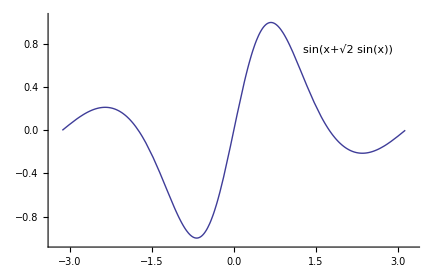

Click the Arrow button on the Drawing Tools palette and place an arrow from the text you just created to the curve:

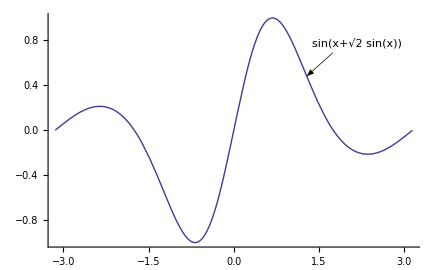

Other tools are available on the Drawing Tools palette for modifying numerous properties of the elements in your graphics, including styles of lines, points and arrows, as well as aligning and grouping graphical elements.

For more information, see the tutorial Drawing Tools.

## Animate

Animating graphics gives a dynamic representation of a process changing over time or dependent upon a parameter.

For example, this animates a plot of the function sin(n x) as n takes on values between 1 and 4:

```mathematica
Animate[
Plot[Sin[n x],{x,0,2π}],
{n,1,4}]
```

Here is an animation of a cuboid centered at {-0.5,-0.5,-0.5}, rotating about the z axis through angles 0≤θ≤2π:

```mathematica
Animate[
Graphics3D[Rotate[Cuboid[{-.5,-.5,-.5}],θ,{0,0,1}],PlotRange->1],
{θ,0,2π}]
```

## Manipulate

You can get a little more control over animations by using a lower-level, but more powerful function, Manipulate.

The basic usage of Manipulate is similar to that of Table.

Here is a simple Manipulate with only one controllable parameter:

```mathematica
Manipulate[
Plot[Sin[n x],{x,0,2π}],
{n,1,4}]
```

This creates a graphic in which you can manipulate three different parameters:

```mathematica
Manipulate[
Plot[a x^2+b x+c,{x,-2,2}],
{a,-2,2},{b,-3,3},{c,-4,4}]
```

This adds labels for each of the parameters:

```mathematica
Manipulate[
Plot[Sin[a x+b]+c,{x,0,6}],
{{a,1,"Frequency"},1,4},
{{b,0,"Phase"},0,10},
{{c,0,"Translate"},-1,1}]
```

You can create a popup list of parameters by making the second argument of Manipulate a list of the form {sym,{e_1,e_2,…,e_n}}:

```mathematica
Manipulate[Plot[f[x],{x,0,2Pi}],{f,{Sin,Cos,Tan,Cot}}]
```

Many more options exist to control the type and placement of various control elements:

```mathematica
Manipulate[
Plot[a Sin[b t],{t,0,2 π},PlotRange-> {-3,3}],
{{a,1,"Amplitude"},1,3},{{b,1,"Frequency"},1,5,1},
ControlPlacement-> Left]
```

```mathematica
Manipulate[
Plot[a Sin[b t],{t,0,2 π},PlotRange-> {-3,3}],
{{a,1,"Amplitude"},1,3},{{b,1,"Frequency"},1,5,1},
ControlPlacement-> {Left,Right},
ControlType->{VerticalSlider,VerticalSlider}]
```

See this tutorial on Manipulate in the Documentation Center for additional information on the many options available for this function.

## Example: Plotting Algebraic Surfaces

Clebsch cubic surfaces are notoriously difficult to represent visually. You will use several graphics options to try and create a publication-quality graphical image.

Here is a first attempt using ContourPlot3D:

```mathematica
clebschSurface=16 x^3+16 y^3-31 z^3+24 x^2 z-48 x^2 y-48 x y^2+24 y^2 z-54 √3 z^2-72 z;ContourPlot3D[clebschSurface,{x,-2.5,2.5},{y,-2.5,2.5},{z,-2.5,2.5}]
```

The default number of contours makes it difficult to see the surface.

You might start to clean up this image by selecting only one contour to begin with:

```mathematica
ContourPlot3D[clebschSurface,{x,-2.5,2.5},{y,-2.5,2.5},{z,-2.5,2.5},Contours->{1}]
```

Now refine the resolution by increasing the number of PlotPoints:

In addition, remove the mesh, as it may obscure certain features:

```mathematica
ContourPlot3D[clebschSurface,{x,-2.5,2.5},{y,-2.5,2.5},{z,-2.5,2.5},Contours->{1},PlotPoints->60,Mesh->None]
```

Now try to adjust various properties of the surface.

Specularity can be used to specify the brightness of the reflection of light on the surface:

```mathematica
ContourPlot3D[clebschSurface,{x,-2.5,2.5},{y,-2.5,2.5},{z,-2.5,2.5},Contours->{1},PlotPoints->60,Mesh->None,ContourStyle->Directive[Orange,Specularity[White,20]]]
```

Finally, remove the box and the axes and add a black background:

```mathematica
ContourPlot3D[clebschSurface,{x,-2.5,2.5},{y,-2.5,2.5},{z,-2.5,2.5},Contours->{1},Mesh->None,PlotPoints->60,ContourStyle->Directive[Orange,Specularity[White,20]],Background->Black,Boxed->False,Axes->False]
```

## Example: Working with Data

This example walks through the steps to import, manipulate, analyze and visualize a set of data.

Start by creating a path to the file you are interested in. It lives in the DataFiles directory that is installed with this course.

```mathematica
datafile=FileNameJoin[{NotebookDirectory[],"data","co2_annmean_mlo.csv"}]
```

Import data measuring atmospheric carbon dioxide levels recorded at Mauna Loa (19°32' N, 155°35' W, 3397 m above MSL) between 1959 and 2020; taken from NOAA (www.esrl.noaa.gov/gmd/ccgg/trends):

```mathematica
data=Import[datafile]
```

This extracts the average annual data: columns 1 and 2 and rows 48 to the end (years 1959 through 2004 and the mean CO2 level):

```mathematica
annualdata=data[[57;;,1;;2]]
```

Here is a plot of the filtered data, using Mesh to show all explicit data points:

```mathematica
dataplot=ListLinePlot[annualdata,Mesh->All]
```

This fits the data with a quadratic model in the parameters a, b, and c:

```mathematica
model=LinearModelFit[annualdata,{1,x,x^2},x]
```

Here is the explicit model:

```mathematica
model["BestFit"]
```

```mathematica
fit[x_]:=model["BestFit"]
```

This plots the fitted function:

```mathematica
fitplot=Plot[fit[x],{x,1959,2005},PlotStyle->{Thick,Pink}]
```

And finally, here is the original data plotted together with the fitted function:

```mathematica
Show[{fitplot,dataplot}]
```

## Exercises

### 3.Subsection Plotting Two Functions Together

Use the Plot function to plot cos(x) and sin(x) on the same graph for x ranging from 0 to 2π.

Hint

Evaluate ?Plot if you need help getting the syntax correct.

Solution

Modify the preceding plot to make the curve for cos(x) red and the curve for sin(x) blue.

Solution

Change the value of the PlotStyle option so that one curve is a dashed black line and the other curve is a thick red line. Thickness and dashing are useful for distinguishing curves in plots that will be printed or displayed in black and white. The dashing of a line is specified using Dashing. The thickness of a line is specified using Thickness.

Hint

Dashing[{0.02}] specifies that lines be drawn using dashes with length equal to 0.02 of the width of the plot. Note that the argument of Dashing is a list.

For example, PlotStyle->Dashing[{0.02}] indicates that the curves in a plot should be drawn as dashed lines.

Thickness[{0.01}] specifies that lines be drawn with thickness equal to 0.01 of the width of the plot.

Can you make one of the lines be both thick and dashed?

Solution

### 3.Subsection Plotting a Surface

Plot the function ⅇ^(-x^2-y^2) using the Plot3D function. Choose what you think are appropriate bounds for x and y to reveal the function being plotted.

Hint

A good choice of ranges to see the basic features of Exp[−x^2−y^2] is {x,−2,2} and {y,−2,2}.

Look up Plot3D in the Help Browser or evaluate ?Plot3D to get information on the correct syntax for the Plot3D function.

Solution

Make a contour plot of this function using the ContourPlot function.

Solution

Make a density plot of this function using the DensityPlot function.

Solution

### 3.Subsection Plotting Data

Evaluate the following input to define data to be a list of 12 pairs of points with coordinate values between 0 and 10:

```mathematica
data=Sort[RandomReal[{0,10},{12,2}]];
```

Use ListLinePlot to plot data as a set of points.

Hint

Evaluate ?ListLinePlot to get information on the correct syntax for ListLinePlot.

Be sure that you have evaluated the input that defines a value for data.

Solution

Include an option to display the points.

Hint

Include the Mesh->All option in your input to ListLinePlot.

Solution

### 3.Subsection Graphics Primitives

Make a plot of 40 circles of unit radius with centers randomly placed in the unit square.

Solution

Make a plot of 200 spheres of unit radius with centers randomly placed in the cube [-10,10]×[-10,10]×[-10,10].

Solution

### 3.Subsection Animation

Evaluate the following input to define a function wheel[{x,y},r,t] that gives the graphics primitives for a disk of radius r centered at the point {x,y} and with a line at angle t to indicate rotation:

```mathematica
wheel[{x_,y_},r_,t_]:={Circle[{x,y},r],Line[{{x+r Cos[t],y+r Sin[t]},{x,y},{x+r Cos[t+π/2],y+r Sin[t+π/2]}}]}
```

Evaluate the following input to see a typical image produced using the wheel function:

```mathematica
Graphics[wheel[{0,0},1,π/8]]
```

Evaluate the following input to generate an animation showing two wheels rotating side by side:

```mathematica
Animate[
Graphics[{wheel[{0,0},1,t],wheel[{3,0},2,t]}],
{t,π/8,4 π,π/8},SaveDefinitions->True]
```

Change this program so that the wheels rotate without slipping. In other words, make one of the wheels rotate in the opposite direction, and make the larger wheel rotate half as fast as the smaller wheel. Try adding a third wheel or changing the characteristics of the wheels.

Hint

The necessary modifications will involve adding only two or three characters to the original program.

Add a minus sign to t in one of the wheel functions so that the wheels will rotate in opposite directions.

Divide t in the second wheel function by 2 so that the larger wheel rotates half as fast, or multiply t in the first wheel function by 2 so that the first wheel rotates twice as fast.

Solution

### 3.Subsection Plotting Regions

Use inequalities to plot the parallelepiped (box) defined by -2≤x≤2, -2≤y≤2 and -1≤z≤1.

Solution

Enclose the box in a sphere that has enough opacity so that you can clearly see the box through the sphere.

Solution

### 3.Subsection Dynamic Taylor Series

Make a dynamic visualization of the Taylor series approximation to the sin function using Manipulate. You will need to plot the sin function together with its Taylor series approximation and vary the number of terms in the polynomial approximation by means of a slider.

Hint

You will need to use the Normal function to convert the output of Series to a regular polynomial that can then be plotted.

```mathematica
Normal[Series[Sin[x],{x,0,5}]]
```

Solution

Modify the preceding visualization so that the user can choose among the three functions: sin, cos, and tan.

Solution